```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
start = 0.1;
time = 0.05;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

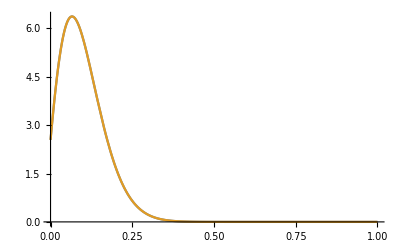

```mathematica
Plot[{Evaluate[Kimura[x,y,t,50]/.{x->start,t -> time}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[Kimura[x,y,t,50]/.{x->start,t -> time}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{8.73514×10^-6}}

```mathematica
Export["SimComparison_neutral_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[Kimura[x,y,t,50]/.{x->start,t -> time, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_neutral_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 2.54376

0.01 xxxx 3.60471

0.02 xxxx 4.5239

0.03 xxxx 5.26614

0.04 xxxx 5.81564

0.05 xxxx 6.17208

0.06 xxxx 6.34661

0.07 xxxx 6.35831

0.08 xxxx 6.23096

0.09 xxxx 5.99052

0.1 xxxx 5.66309

0.11 xxxx 5.27344

0.12 xxxx 4.84401

0.13 xxxx 4.39429

0.14 xxxx 3.9406

0.15 xxxx 3.49599

0.16 xxxx 3.07048

0.17 xxxx 2.67126

0.18 xxxx 2.3031

0.19 xxxx 1.96869

0.2 xxxx 1.66904

0.21 xxxx 1.40384

0.22 xxxx 1.17178

0.23 xxxx 0.970845

0.24 xxxx 0.798587

0.25 xxxx 0.652285

0.26 xxxx 0.529127

0.27 xxxx 0.426332

0.28 xxxx 0.34123

0.29 xxxx 0.27133

0.3 xxxx 0.214355

0.31 xxxx 0.168261

0.32 xxxx 0.131239

0.33 xxxx 0.101717

0.34 xxxx 0.0783392

0.35 xxxx 0.0599557

0.36 xxxx 0.045598

0.37 xxxx 0.0344606

0.38 xxxx 0.0258793

0.39 xxxx 0.0193118

0.4 xxxx 0.0143192

0.41 xxxx 0.0105493

0.42 xxxx 0.00772157

0.43 xxxx 0.0056149

0.44 xxxx 0.00405603

0.45 xxxx 0.00291035

0.46 xxxx 0.00207413

0.47 xxxx 0.00146801

0.48 xxxx 0.00103175

0.49 xxxx 0.000719987

0.5 xxxx 0.00049879

0.51 xxxx 0.000342998

0.52 xxxx 0.00023409

0.53 xxxx 0.000158532

0.54 xxxx 0.000106516

0.55 xxxx 0.00007099

0.56 xxxx 0.0000469215

0.57 xxxx 0.0000307499

0.58 xxxx 0.000019976

0.59 xxxx 0.0000128605

0.6 xxxx 8.203×10^-6

0.61 xxxx 5.18232×10^-6

0.62 xxxx 3.24172×10^-6

0.63 xxxx 2.00716×10^-6

0.64 xxxx 1.22965×10^-6

0.65 xxxx 7.45091×10^-7

0.66 xxxx 4.46352×10^-7

0.67 xxxx 2.64234×10^-7

0.68 xxxx 1.545×10^-7

0.69 xxxx 8.91793×10^-8

0.7 xxxx 5.0786×10^-8

0.71 xxxx 2.85164×10^-8

0.72 xxxx 1.57767×10^-8

0.73 xxxx 8.59372×10^-9

0.74 xxxx 4.60503×10^-9

0.75 xxxx 2.42536×10^-9

0.76 xxxx 1.25423×10^-9

0.77 xxxx 6.36144×10^-10

0.78 xxxx 3.16066×10^-10

0.79 xxxx 1.53618×10^-10

0.8 xxxx 7.29254×10^-11

0.81 xxxx 3.37521×10^-11

0.82 xxxx 1.52014×10^-11

0.83 xxxx 6.64602×10^-12

0.84 xxxx 2.81331×10^-12

0.85 xxxx 1.14508×10^-12

0.86 xxxx 4.48086×10^-13

0.87 xxxx 1.68532×10^-13

0.88 xxxx 5.61773×10^-14

0.89 xxxx 1.90958×10^-14

0.9 xxxx 7.99361×10^-15

0.91 xxxx 1.11022×10^-15

0.92 xxxx 1.28786×10^-14

0.93 xxxx -5.55112×10^-15

0.94 xxxx -3.77476×10^-15

0.95 xxxx -3.77476×10^-15

0.96 xxxx -5.55112×10^-15

0.97 xxxx -1.55431×10^-14

0.98 xxxx -1.22125×10^-14

0.99 xxxx 4.13003×10^-14

1. xxxx 0.